```mathematica
ClearAll[files, importfile, raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/322(4.8)/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/322(4.8)/f1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/322(4.8)/~$Книга1.xlsx}

```mathematica
importfile = files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/322(4.8)/Книга1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

```mathematica
dataset1=makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"x"->(Around[#x,#dx]&),"L"->(Around[#L,#dL]&)|>]
```

Dataset[<>]

```mathematica
dataset2=makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"x"->(Around[#x,#dx]&),"L"->(Around[#r,#dr]&)|>]
```

Dataset[<>]

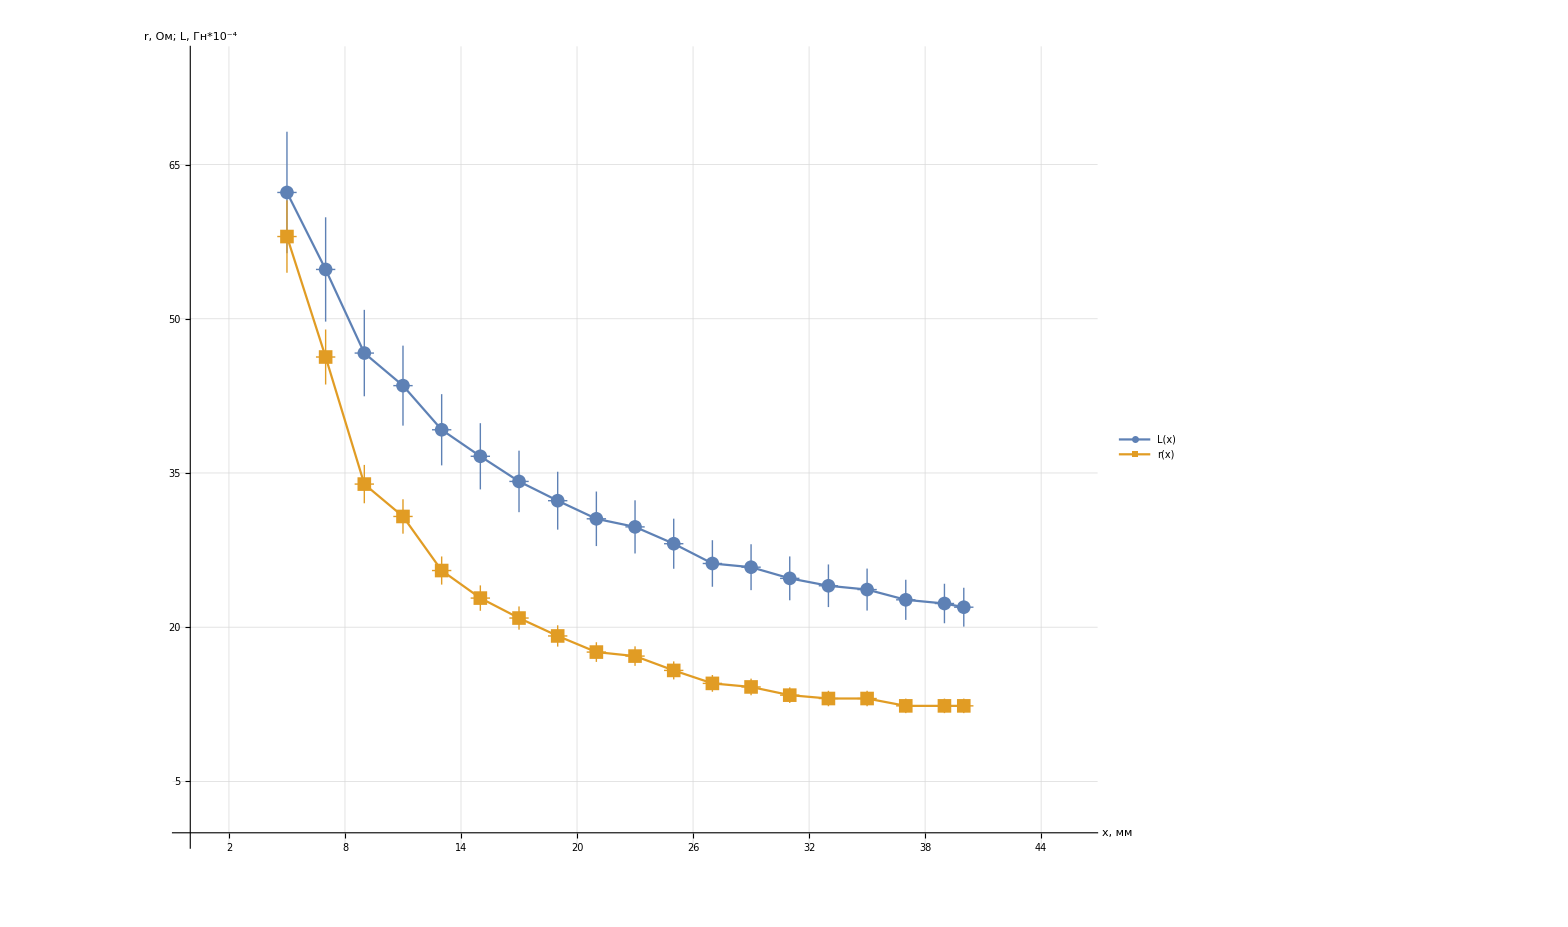

```mathematica
Show[
ListPlot[
{dataset1WithErrs,dataset2WithErrs},
Joined->True,
AxesLabel->{Style["x, мм",Large],Style["r, Ом; L, Гн*10^-4",Large]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->1500,
GridLines->{Range[-10,430,1], Range[-10,500,2]},
Ticks-> {Range[-10,420,2],Range[-10,500,5]}, 
TicksStyle->20,
PlotRange->{{0,46},{0,75}},
PlotMarkers->{Automatic,14},
PlotLegends->Placed[LineLegend[
Automatic,
{"L(x)", " r(x)"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.6],Scaled[0.6]}
]
]
]
```

```mathematica
Vector
```